Coax Cylinders

Numerical Solution - Potential

```mathematica
ncoaxpdata = Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/problem1.dat"]
```

{}

```mathematica
ncoaxpdata = Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/problem1.dat"];
ncoaxpdatareshape = ArrayReshape[ncoaxpdata, {250,250}];
epilog=ListContourPlot[ncoaxpdatareshape,ContourShading->None, Contours->Function[{min,max},Range[min,max,5]]][[1]];
numerical1 = ListDensityPlot[ncoaxpdatareshape,PlotTheme->"Detailed",PlotLabel->"Iterations=100,000", ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), Epilog->epilog,ImageSize->Large]
```

-Graphics-

Voltage = 100
Grid = 250
Large cylinder = 100
Small cylinder = 20
Method = FDM

- Create a GIF (Potential )

```mathematica
Do[Export["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/anim/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/anim/" <> ToString[i] <> ".dat"],{250,250}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/anim/" <> ToString[i] <> ".dat"], {250,250}],ContourShading->None, Contours->Function[{min,max},Range[min,max,5]]][[1]],PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 10000, 10}]
```

Numerical Solution - Electric Field

```mathematica
coaxedata = Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/electricField.dat"];
coords = data[[All, {1, 2}]];
comps = data[[All, {3, 4}]];
out = Thread[{coords, comps}];
s2 = ListVectorPlot[out, VectorScale->{0.01, Automatic,None}, VectorPoints->50, VectorStyle->Red];
```

```mathematica
Show[s1, s2, PlotRange-> All]
```

Analytical Solution

```mathematica
analytical[x_, y_] = (100 * Log[(x^2+y^2)/20])/Log[5]
```

(100 Log[1/20 (x^2+y^2)])/Log[5]

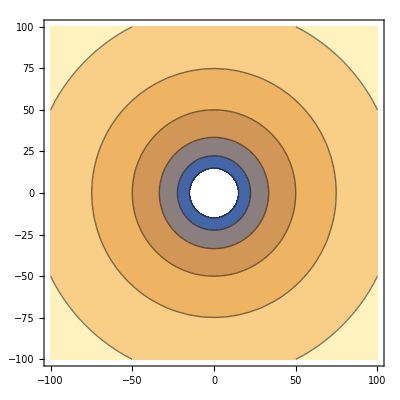

```mathematica
analytical_sol = ContourPlot[analytical[x,y], {x, -100, 100}, {y, -100, 100}]
```

```mathematica
coords = data[[All, {1, 2}]];
comps = data[[All, {3, 4}]];
out = Thread[{coords, comps}];
```

# Analytical Solution - Potential (using C++)

```mathematica
acoaxpdata= Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/coax_anal.dat"];

acoaxpreshape = ArrayReshape[acoaxpdata, {250,250}];
```

```mathematica
epilog2=ListContourPlot[acoaxpreshape,ContourShading->None, Contours->Function[{min,max}, Range[min,max,5]]][[1]];ListDensityPlot[acoaxpreshape,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), Epilog->epilog2, ImageSize->Large]
```

-Graphics-

```mathematica
Export["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/analytical_coax.png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/coax_anal.dat"],{250,250}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/coax_anal.dat"], {250,250}],ContourShading->None, Contours->Function[{min,max},Range[min,max,5]]][[1]]]]
```

/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/analytical_coax.png

Analytical Solution - Electric field (using C++)

```mathematica
ClearAll["Global`*"]

data = Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/coax_ef.dat","Table"]
coords = data[[All,{1,2}]];
comps = data[[All,{3,4}]];
out = Thread[{coords,comps}];
```

{{-100,-100,6.93865,6.93865},{-100,-99,6.91556,6.91556},{-100,-98,6.89255,6.89255},{-100,-97,6.86962,6.86962},{-100,-96,6.84678,6.84678},{-100,-95,6.82402,6.82402},{-100,-94,6.80135,6.80135},{-100,-93,6.77876,6.77876},{-100,-92,6.75627,6.75627},{-100,-91,6.73388,6.73388},39981,{99,91,-6.77713,-6.77713},{99,92,-6.79991,-6.79991},{99,93,-6.82279,-6.82279},{99,94,-6.84577,-6.84577},{99,95,-6.86883,-6.86883},{99,96,-6.89198,-6.89198},{99,97,-6.91522,-6.91522},{99,98,-6.93854,-6.93854},{99,99,-6.96194,-6.96194}}
 |  |  |  |

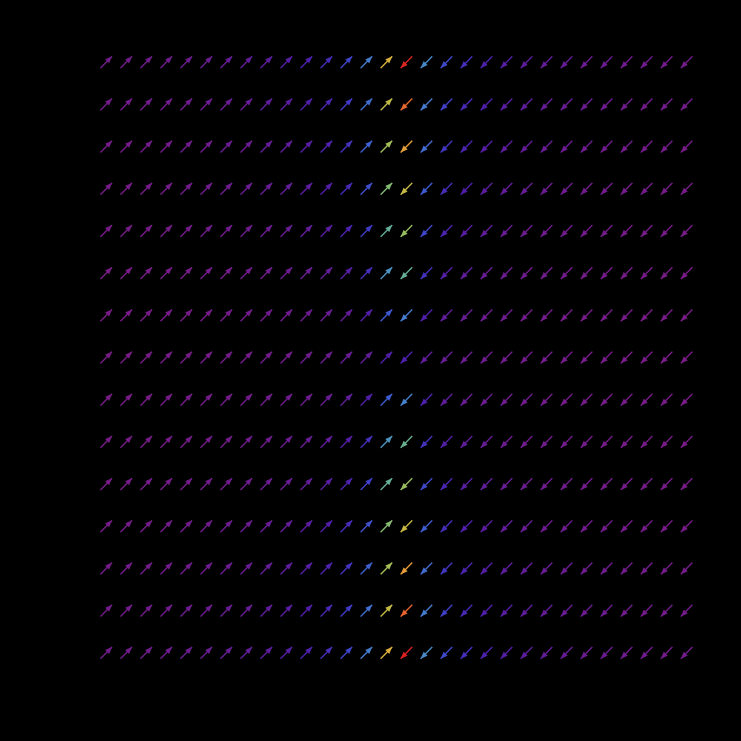

```mathematica
eField = ListVectorPlot[out,
VectorScale->{0.02,Automatic,None},
VectorStyle->Thick,
VectorPoints->{30,15},
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality",
AspectRatio->1
]
```

# - Compare analytical solution to numerical solution (Potential)

```mathematica
comparep = ncoaxpdatareshape - acoaxpreshape
```

{1}
 |  |  |  |

```mathematica
(*epilog2=ListContourPlot[comparep,ContourShading->None][[1]];*)
ListDensityPlot[comparep,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), ImageSize->Large, PlotLabel->"Iterations = 10,000"]
```

-Graphics-

- Comparison GIF

```mathematica
Do[Export["/home/2317101h/year_3/group_project/compare/coax/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/anim/" <> ToString[i] <> ".dat"],{250,250}] - ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/coax_cyl/coax_anal.dat"],{250,250}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 10000, 10}]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}gif
```